## Setup

This setup uses (n,η) variables instead of (ρ,η).

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{fhat_,uSource_,vSource_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]
+(eps (uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Eqs"->{
Dv discreteLaplace[etaVec,L/gridRes]
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
Dv (1+Du/Dv) discreteLaplace[etaVec,L/gridRes]
-Du discreteLaplace[nVec,L/gridRes]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Jacobian

```mathematica
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
laplaceMatrixS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
Options@constructGluedJacobianAS={"Reverse"->False};
constructGluedJacobianAS[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
With[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixAS[gridRes],{{0,Dv},{-Du,Dv(1+Du/Dv)}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

```mathematica
constructGluedJacobianS[fdSetup_,params_,statSol_,dfdu_]:=
With[{
solVec=Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixS[gridRes],{{0,Dv},{-Du,Dv(1+Du/Dv)}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

### Finite-differences setup for the mass-conserving system

```mathematica
ClearAll@setupFiniteDifferenceEqsMC;
setupFiniteDifferenceEqsMC[f_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Eqs"->{
Du discreteLaplace[nVec,L/gridRes]+(f/.{n->nVec,η->eta}),
Total@nVec-gridRes p
}
|>
]
```

```mathematica
getInitGuessMC[fdSetup_,params_,initSol_,Teval_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,Teval]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{eta,eta[0,Teval]/.params/.initSol}}
]
```

### Model setup

Const-reaction-rate reaction kinetics in (n,η) variables

```mathematica
f=(η-n^3+n);
source=(p-n);
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[{f,source,0},200];
fdSetupMC=setupFiniteDifferenceEqsMC[f,200];
```

```mathematica
fixedParams={p->-2/10,Du->1,L->40/2,T->10000};
params=Join[{eps->10^(-3),Dv->1000},fixedParams];
```

```mathematica
rhobar=-2/10;
```

```mathematica
dx[fdSetup_]:=L*(fdSetup["UnitGrid"][[2]]-fdSetup["UnitGrid"][[1]]);
```

## Mass-conserving

#### Stat. state

```mathematica
initRunMC=runTwoComponentSim[
{f,0,0},
params,
{
(rhobar+0.5*Cos[Pi*#/L])&,
0&
},
T/10/.fixedParams
];
```

```mathematica
statSolMC=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.p->rhobar/.params,
getInitGuessMC[fdSetupMC,params,initRunMC,T/10/.params],
AccuracyGoal->10,
PrecisionGoal->10,
WorkingPrecision->100,
MaxIterations->100
]
];
```

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

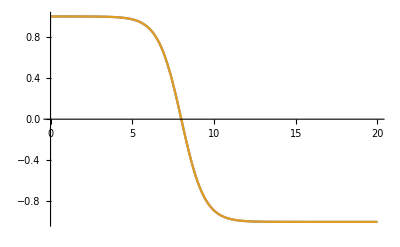

```mathematica
Plot[{Interpolation[Transpose@{fdSetupMC["UnitGrid"]*L/.params,fdSetupMC["nVec"]/.statSolMC}][x],n[x,T/10]/.params/.initRunMC},{x,0,L/.params},
PlotRange->All]
```

#### Modes

```mathematica
{evalsMC,evecsMC}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianAS[
fdSetup,
params,
Join[Thread[fdSetup["etaVec"]->(eta/.statSolMC)],DeleteCases[statSolMC,eta->_]],
D[{0,-f},{{n,η}}],
"Reverse"->False
],-5,Method->{"Arnoldi",Tolerance->10^-20}],#[[1]]&];
```

```mathematica
evalsMC
```

6.9019997756150733828989866248422460517464060374074541499426194690979883679539961269291049102916178401×10^-9

Zero mode

```mathematica
{evalsMCS,evecsMCS}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianS[
fdSetup,
params,
Join[Thread[fdSetup["etaVec"]->(eta/.statSolMC)],DeleteCases[statSolMC,eta->_]],
D[{0,-f},{{n,η}}]
],-6,Method->{"Arnoldi",Tolerance->10^-20}],#[[1]]&];
```

```mathematica
evalsMCS
```

2.9265478815242152447157301474569937151557952998946467249851940727625332448678164177691826358060783107×10^-120

```mathematica
massCompDModeNorm=evecsMC[[;;;;2]]/(dx[fdSetupMC]*Total[evecsMC[[;;;;2]]])/.params;
massCompEtaModeNorm=evecsMC[[2;;;;2]]/(dx[fdSetupMC]*Total[evecsMC[[;;;;2]]])/.params;
```

```mathematica
massDModeNorm=evecsMCS[[;;;;2]]/(dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params;
dEtadM=Mean[evecsMCS[[2;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params];
```

```mathematica
dEtadM
```

-8.53613×10^-10

```mathematica
translMode=Differences[Join[{#[[1]]},#,{#[[-1]]}],1,2]&@fdSetupMC["nVec"]/.statSolMC;
translDModeNorm=translMode/(dx[fdSetupMC]*Total[translMode])/.params;
```

```mathematica
lInt=(dx[fdSetupMC]*Total[massDModeNorm^2])^-1/.params
```

4.24052

```mathematica
xiP=(rhobar+1)/2
xiM=1-xiP
```

2/5

3/5

As the outer tail is much shorter than the inner one, dEtadM approximates (∂^+)_M etastat.
Then, Eq. (30) gives

```mathematica
σAnalytic=-dEtadM/(xiM L/(2*Dv)+(1+Du/Dv)/(2*lInt))/.params
```

6.88242×10^-9

#### Plots

```mathematica
intPos=First@FirstPosition[fdSetupMC["UnitGrid"],x_/;(x>xiP)]
```

81

Approximation of the δη(x) profile, Eq. (E9b), determined using Eq. (E10)

```mathematica
etaApprox=Join[
Array[1&,intPos-1],
(1-fdSetupMC["UnitGrid"][[intPos;;]])/xiM,
-Reverse[(1-fdSetupMC["UnitGrid"][[intPos;;]])/xiM],
-Reverse@Array[1&,intPos-1]
]*xiM*L*σAnalytic/Dv/.params;
```

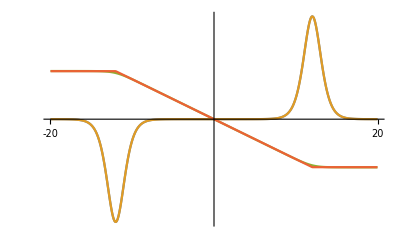

```mathematica
ListLinePlot[Transpose/@{{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-massCompDModeNorm,Reverse@massCompDModeNorm]},{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-massDModeNorm,Reverse@massDModeNorm]},
{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,2*10^9*Join[-massCompEtaModeNorm,Reverse@massCompEtaModeNorm]},
{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,2*10^9*etaApprox}},
PlotRange->All,
Ticks->{{-L,L}/.params,{-5,5}}]
```

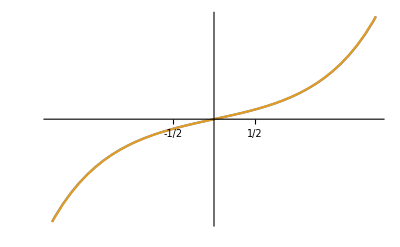

```mathematica
ListLinePlot[Transpose/@{{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-massCompDModeNorm,Reverse@massCompDModeNorm]},{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-translDModeNorm,Reverse@translDModeNorm]}},
PlotRange->{{-L/10,L/10}/.params,{-10^-6,10^-6}},
Ticks->{{-1/2,1/2},{-5,5}}]
```

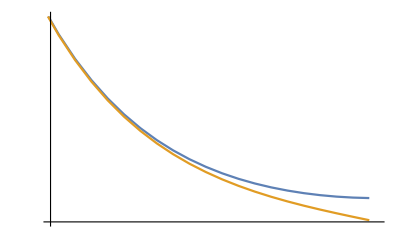

```mathematica
ListLinePlot[Transpose/@{{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-massCompDModeNorm,Reverse@massCompDModeNorm]},{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-translDModeNorm,Reverse@translDModeNorm]}},
PlotRange->{{9L/10,L}/.params,{0,3*10^-4}},
Ticks->{{-1/2,1/2},{-5,5}}]
```

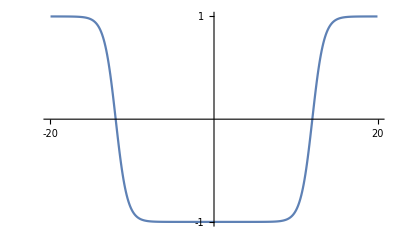

```mathematica
ListLinePlot[Transpose@{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[fdSetupMC["nVec"],Reverse@fdSetupMC["nVec"]]/.statSolMC},
PlotRange->All,
Ticks->{{-L,L}/.params,{-1,1}}]
```

## Non mass-conserving

#### Stat. state

```mathematica
initRunLS=runTwoComponentSim[
{f,source,0},
params,
{
(rhobar+0.1*Cos[Pi*#/L])&,
0&
},
T/.fixedParams
];
```

```mathematica
statSolLS=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRunLS],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100,
MaxIterations->100
]
];
```

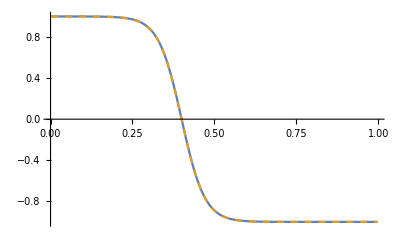

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.params/.initRunLS}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.statSolLS}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

#### Modes

```mathematica
{evalsLS,evecsLS}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianAS[
fdSetup,
params,
statSolLS,
D[{eps source,-f+Du/Dv eps source},{{n,η}}],
"Reverse"->False
],-5,Method->{"Arnoldi",Tolerance->10^-20}],#[[1]]&];
```

```mathematica
SetPrecision[evalsLS,6]
```

-0.0000291175

```mathematica
massCompDModeNormLS=evecsLS[[;;;;2]]/(dx[fdSetup]*Total[evecsLS[[;;;;2]]])/.params;
massCompEtaModeNormLS=evecsLS[[2;;;;2]]/(dx[fdSetup]*Total[evecsLS[[;;;;2]]])/.params;
```

```mathematica
translModeLS=Differences[Join[{#[[1]]},#,{#[[-1]]}],1,2]&@fdSetup["nVec"]/.statSolLS;
translDModeNormLS=translModeLS/(dx[fdSetupMC]*Total[translModeLS])/.params;
```

```mathematica
σD=-2*Dv/(xiM L)*dEtadM/.params
σR=-2*lInt*dEtadM/(1+Du/Dv)/.params
```

1.42269×10^-7

7.23229×10^-9

Eq. (39)

```mathematica
σAnalyticLS=(σD-eps(1-p)/2)/(1+σD/σR)/.params
```

-0.0000290188

Eq. (G2)

```mathematica
dEta=-xiM L/Dv(σAnalyticLS + eps)/.params
```

-0.0000116518

#### Plots

```mathematica
intPos=First@FirstPosition[fdSetup["UnitGrid"],x_/;(x>xiP)]
```

81

```mathematica
etaApproxLS=Join[
Array[1&,intPos-1],
(1-fdSetupMC["UnitGrid"][[intPos;;]])/xiM,
-Reverse[(1-fdSetupMC["UnitGrid"][[intPos;;]])/xiM],
-Reverse@Array[1&,intPos-1]
]*(-dEta)/.params;
```

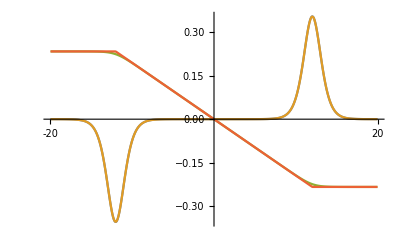

```mathematica
ListLinePlot[Transpose/@{{Join[-L*Reverse@fdSetup["UnitGrid"],L*fdSetup["UnitGrid"]]/.params,Join[-massCompDModeNormLS,Reverse@massCompDModeNormLS]},{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[-translDModeNormLS,Reverse@translDModeNormLS]},
{Join[-L*Reverse@fdSetup["UnitGrid"],L*fdSetup["UnitGrid"]]/.params,
20000*Join[-massCompEtaModeNormLS,Reverse@massCompEtaModeNormLS]},
{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,20000*etaApproxLS}},
PlotRange->All,
Ticks->{{-L,L}/.params,None}]
```

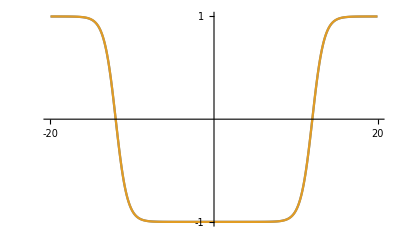

```mathematica
ListLinePlot[Transpose/@{{Join[-L*Reverse@fdSetup["UnitGrid"],L*fdSetup["UnitGrid"]]/.params,Join[fdSetup["nVec"],Reverse@fdSetup["nVec"]]/.statSolLS},{Join[-L*Reverse@fdSetupMC["UnitGrid"],L*fdSetupMC["UnitGrid"]]/.params,Join[fdSetupMC["nVec"],Reverse@fdSetupMC["nVec"]]/.statSolMC}},
PlotRange->All,
Ticks->{{-L,L}/.params,{-1,1}}]
```

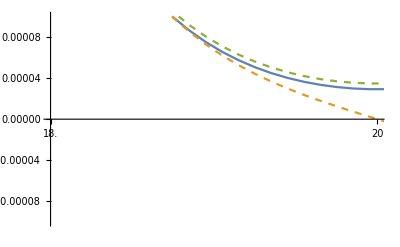

```mathematica
ListLinePlot[Transpose/@{{L*Join[fdSetup["UnitGrid"],{2-fdSetup["UnitGrid"][[-1]]}]/.params,Join[Reverse@massCompDModeNormLS,{massCompDModeNormLS[[1]]}]},{L*Join[fdSetupMC["UnitGrid"],{2-fdSetup["UnitGrid"][[-1]]}]/.params,Join[Reverse@translDModeNorm,{-translDModeNorm[[1]]}]},{L*Join[fdSetupMC["UnitGrid"],{2-fdSetup["UnitGrid"][[-1]]}]/.params,Join[Reverse@massDModeNorm,{massDModeNorm[[1]]}](*-eps Abs[p-1]/(4*Dv)xiP L/.params*)}},
PlotRange->{{0.9L,L}/.params,{- 10^-4,10^-4}},
Ticks->{{0.9 L,L}/.params,None},
PlotStyle->{Automatic,Dashed,Dashed}]
```